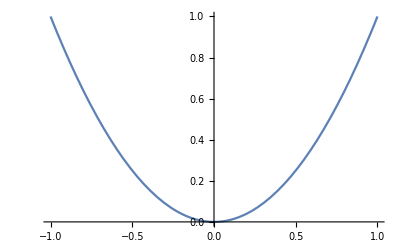

```mathematica
Plot[x^2,{x,-1,1}]
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Aspect Ratio de 1:2 *)
```

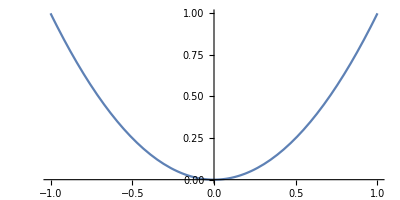

```mathematica
Plot[x^2,{x,-1,1},AspectRatio->.5]
```

```mathematica
(* Aspect Ratio de 2:1 *)
```

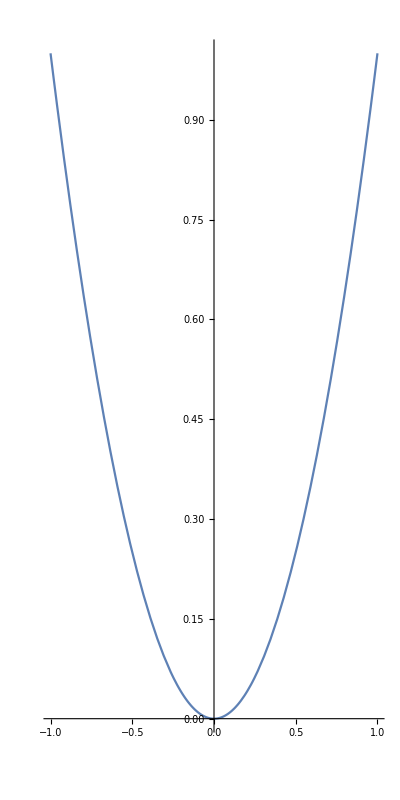

```mathematica
Plot[x^2,{x,-1,1},AspectRatio->2]
```

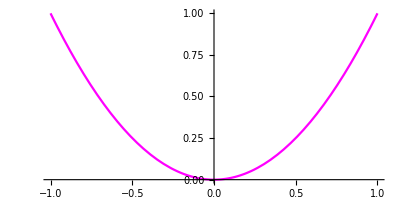

```mathematica
(* Usando o PlotStyle para mudar as cores do gráfico *)
Plot[x^2,{x,-1,1},AspectRatio->.5,PlotStyle->Magenta]
```

```mathematica
(* Usando GridLines *)
```

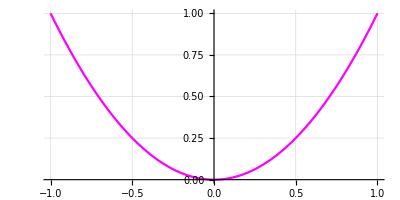

```mathematica
Plot[x^2,{x,-1,1},AspectRatio->.5,PlotStyle->Magenta,GridLines->Automatic]
```

```mathematica
Plot[x^2,{x,-1,1},AspectRatio->.5,PlotStyle->Magenta,GridLines->Automatic,GridLinesStyle->{{Red,Dotted,Thick},{Gray,Dotted}}]
```

-Graphics-

```mathematica
(* BoxRaios na razão de 1:1:1 *)
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
(* BoxRaios na razão de 1:1:1 *)
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},BoxRatios->{1,1,.5}]
```

-Graphics3D-

```mathematica
(* Usando Filling *)
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},Filling->Bottom]
```

-Graphics3D-

```mathematica
(* Aplicando o FillingStyle *)
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},Filling->Bottom,FillingStyle->Opacity[.8],PlotStyle->Red]
```

-Graphics3D-

```mathematica
(* BoundaryStyle *)
```

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},BoundaryStyle->{Thick,RGBColor[0,255,255]}]
```

-Graphics3D-

```mathematica
(* Exemplos com PlotStyle *)
```

```mathematica
Plot3D[x^3+y^3,{x,-1,1},{y,-1,1},PlotStyle->{Green},BoundaryStyle->{Thick,Blue},Filling->Bottom,FillingStyle->{Opacity[.2]},BoxRatios->{1,1,3}]
```

-Graphics3D-

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},PlotStyle->{LightBlue},BoundaryStyle->{Thick,Blue},Filling->Bottom,FillingStyle->{Opacity[.2]}]
```

-Graphics3D-

```mathematica
(* ContourPlot *)
```

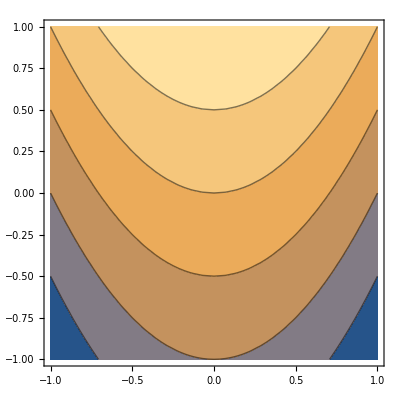

```mathematica
ContourPlot[y-x^2,{x,-1,1},{y,-1,1}]
```

```mathematica
(* ContourPlot com ContourShading False para remover o gradiente de cores *)
```

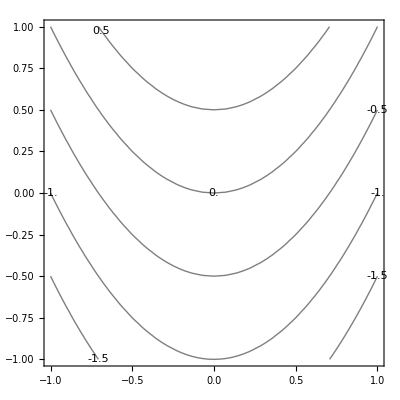

```mathematica
ContourPlot[y-x^2,{x,-1,1},{y,-1,1},ContourLabels->True,ContourShading->False]
```

```mathematica
(* Contorno y-x^2=k com k=0 *)
```

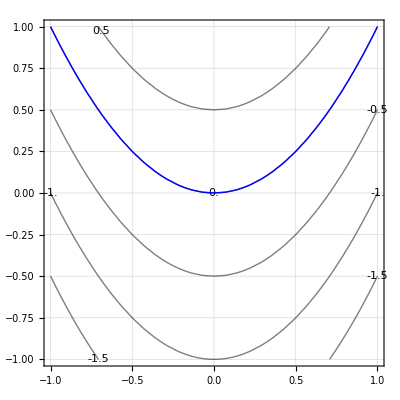

```mathematica
Show[ContourPlot[{y-x^2},{x,-1,1},{y,-1,1},ContourLabels->True,ContourShading->False,GridLines->Automatic],ContourPlot[y-x^2==0,{x,-1,1},{y,-1,1},ContourStyle->{Thick,Blue}]]
```

```mathematica
superficie=ContourPlot3D[z==y-x^2,{x,-1,1},{y,-1,1},{z,-1.6,.6}, ContourStyle->{Blue,Opacity[0.3]},BoundaryStyle->{Thick,Blue}];
```

```mathematica
superficie2=ContourPlot3D[0==y-x^2,{x,-1,1},{y,-1,1},{z,-1.6,.6},ContourStyle->{Red,Opacity[0.3]},BoundaryStyle->{Thick,Red}];
```

```mathematica
Show[superficie,superficie2]
```

-Graphics3D-

```mathematica
superficie=ContourPlot3D[z==y-x^2,{x,-1,1},{y,-1,1},{z,-1.6,.6},ContourStyle->{Blue,Opacity[0.3]},BoundaryStyle->{Thick,Blue},Mesh->None,PlotPoints->100];
```

```mathematica
superficie2=ContourPlot3D[0==y-x^2,{x,-1,1},{y,-1,1},{z,-1.6,.6},ContourStyle->{Red,Opacity[0.3]},BoundaryStyle->{Thick,Red},Mesh->None];
```

```mathematica
curve=ContourPlot3D[y-x^2==0,{x,-1,1},{y,-1,1},{z,-.00001,.00001},ContourStyle->{Red,Opacity[0.3]},BoundaryStyle->{Thickness[.01],Black},Mesh->None];
```

```mathematica
plan=ParametricPlot3D[{x,y,0},{x,-1,1},{y,-1,1},Mesh->None,BoundaryStyle->{Thick,Green},PlotStyle->{Opacity[.3],Green}];
```

```mathematica
(* Interseção das duas superfícies com o plano z=0 representando uma solução *)
```

```mathematica
Show[superficie,superficie2,plan,curve]
```

-Graphics3D-

```mathematica
(* Parametrização de circunferência *)
```

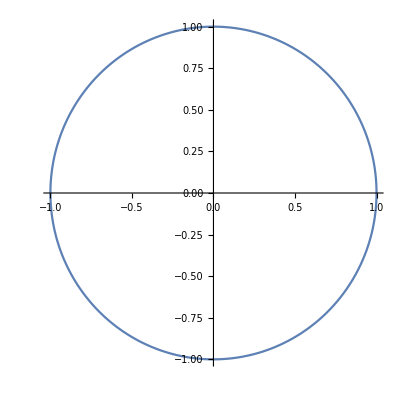

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}]
```

```mathematica
(* Ponto tangenciado a circunferência *)
```

```mathematica
Manipulate[Show[ParametricPlot[{Sin[t],Cos[t]},{t,0,2 Pi}],Graphics[{PointSize[Large],Point[{Sin[κ],Cos[κ]}]}]],{κ,0,2π}]
```

```mathematica
(* Usando a mesma ideia para um vetor [Trajetória elíptica] *)
```

```mathematica
γ[t_]:={ 2Sin[t],Cos[t]}
```

```mathematica
trajetoria = ParametricPlot[γ[t],{t,0,2π},PlotStyle->Thin];
```

```mathematica
(* Fazendo um vetor *)
```

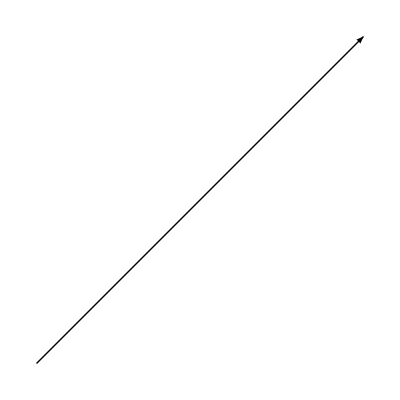

```mathematica
Graphics[Arrow[{{0,0},{1,1}}]]
```

```mathematica
(* Generalizando o vetor como função de t *)
```

```mathematica
(* Sabemos que o vetor deve tangenciar a curva e, como γ representa um ponto no espaço vamos precisar dar um comprimento que seja visível quando o vetor for renderizado *)
```

```mathematica
vetor = Graphics[Arrow[{γ[t],γ[t]+.2γ'[t]}]];
```

```mathematica
(* O resultado abaixo mostra que ao multiplicar por .2 a derivada de γ em relação a t demos o comprimento da Arrow que vai do ponto γ[t] ao ponto γ[t]+.2γ'[t]. A derivada temporal é essencial nesse caso, e podemos considerá-la essencial para a mudança de direção do vetor, dado que para cada ponto γ[t] o ângulo medido é distinto e fornece diferentes módulos do vetor velocidade *)
```

```mathematica
Manipulate[Graphics[Arrow[{γ[t],γ[t]+.2γ'[t]}]],{t,0,2Pi}]
```

```mathematica
Manipulate[Show[trajetoria,Graphics[Arrow[{γ[t],γ[t]+.2γ'[t]}]]],{t,0,2Pi}]
```

```mathematica
(* Se multiplicarmos por .4 a derivada será possível ver mais claramente a mudança da intensidade do vetor velocidade ao chegar nas extremidade de menor raio de curvatura da trajetória elíptica *)
```

```mathematica
Manipulate[Show[trajetoria,Graphics[Arrow[{γ[t],γ[t]+.4γ'[t]}]]],{t,0,2Pi}]
```

```mathematica
(* Espiral *)
```

```mathematica
a=ParametricPlot3D[{Sin[t],Cos[t],t},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
(* Pontos *)
```

```mathematica
b=Graphics3D[{PointSize[Large],Red,Point[{{0,1,0},{0,1,2 Pi}}]}]
```

-Graphics3D-

```mathematica
(* Espiral com pontos *)
```

```mathematica
Show[a,b]
```

-Graphics3D-

```mathematica
(* Vetor tangente à curva no espaço *)
```

```mathematica
η[t_]:={Sin[t],Cos[t],t}
```

```mathematica
Manipulate[Show[a,b,Graphics3D[Arrow[{η[t],η[t]+.2η'[t]}]]],{t,0,2π}]
```

```mathematica
(* Aumentando o número de voltas da espira *)
```

```mathematica
a1=ParametricPlot3D[{Sin[t],Cos[t],t},{t,0,10 Pi},BoxRatios->{1, 1, .5},PlotStyle->{Thin,Dashed,Red}];
```

```mathematica
b1=Graphics3D[{PointSize[Large],Red,Point[{{0,1,0},{0,1,10 Pi}}]}];
```

```mathematica
Manipulate[Show[a1,b1,Graphics3D[{Arrowheads[.005],Arrow[{η[t],η[t]+.4η'[t]}]}]],{t,0,10π}]
```